```mathematica
Quiet@Remove["Global`*"];
```

x = -(1-π^2)/(-1+π^2) y= 0

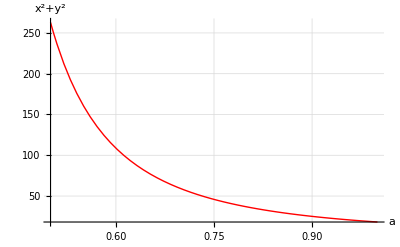

```mathematica
sol = Solve[{a*x + y == Pi, x + Pi*y == 1}, {x,y}][[1]];
exprtodraw = x^2+y^2/.sol;
a = Pi;
Print["x = ", x/.sol," y= ", y/.sol]
plot = Plot[exprtodraw, {a, 0.5, 1},AxesLabel->{"a", "x^2+y^2"}, GridLines->Automatic, PlotStyle->{Red, Thick}]
```

```mathematica
Quiet@Remove["Global`*"];
```

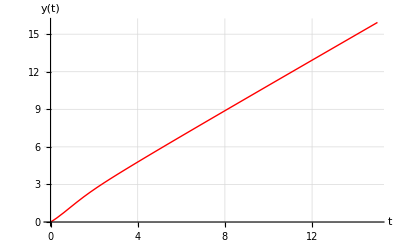

```mathematica
eqn = {y'[t] + (t+1)*y[t] == t, y[0] == 0};
sol = DSolve[eqn, y[t], t][[1]];
result = y[t]/.sol;
Plot[{result + t}, {t, 0, 15}, AxesLabel->{"t", "y(t)"}, GridLines->Automatic, PlotStyle->{Red, Thick}]
```

```mathematica
(*I would start at 2 because it seems to be an approximate value of the root*)
t0 = t/.FindRoot[{result == 0.6}, {t, 2}];
Print["t0 = ", t0]
```

t0 = 1.99083